## Problem 2 Calculations

Temporal Discritezations:

```mathematica
sf = Solve[(u[n+1]-u[n])/Δt==γ u[n],u[n+1]];
evalFE = Simplify[(u[n+1]/.sf)/u[n]][[1]]
```

1+γ Δt

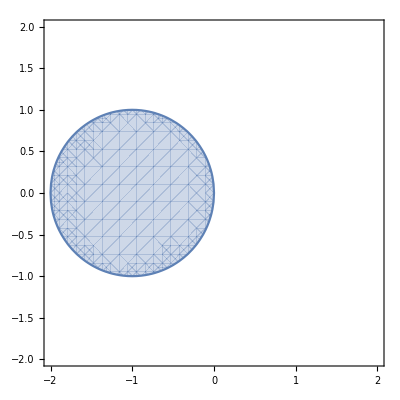

```mathematica
fz = evalFE/. γ Δt -> z;
ComplexRegionPlot[Abs[fz]≤ 1, {z, -2-2 ⅈ, 2+2 ⅈ}]
```

```mathematica
(*Backward Euler in Time *)
sb = Solve[(u[n]-u[n-1])/Δt==γ u[n],u[n]];
evalBE = Simplify[(u[n]/.sb)/u[n-1]][[1]]
```

1/(1-γ Δt)

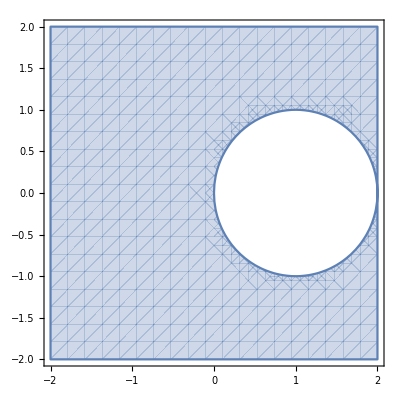

```mathematica
bz = evalBE/. γ Δt -> z;
ComplexRegionPlot[Abs[bz]< 1, {z, -2-2 ⅈ, 2+2 ⅈ}]
```

```mathematica
(* Central difference in time *)
(* Au = λ u *)
A = {{(2 γ  Δt),1},{1, 0}};
evals = Eigenvalues[A]
```

{γ Δt-√(1+γ^2 Δt^2),γ Δt+√(1+γ^2 Δt^2)}

```mathematica
cz = evals/. {γ -> z,Δt -> 1};
ComplexRegionPlot[{Abs[cz[[1]]]≤ 1&&Abs[cz[[2]]]≤ 1}, {z, -2-2 ⅈ, 2+2 ⅈ}]
```

-Graphics-

Spatial Discritizations:

```mathematica
n = 25;
```

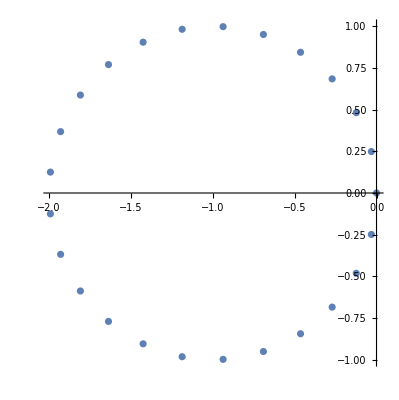

```mathematica
Dp = DiagonalMatrix[Table[-1/Δx,{i,1,n}]] + DiagonalMatrix[Table[1/Δx,{i,1,n-1}],1];
Dp[[n]][[1]] = 1/Δx;
Dp//MatrixForm;
Dpevals = Eigenvalues[Dp];
Dpz = Dpevals /. Δx -> 1;
fsplot = ComplexListPlot[Dpz]
```

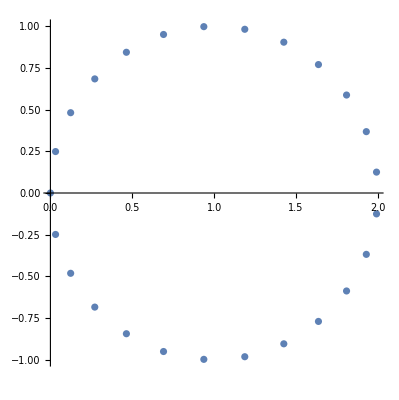

```mathematica
Dm= DiagonalMatrix[Table[1/Δx,{i,1,n}]] + DiagonalMatrix[Table[-1/Δx,{i,1,n-1}],-1];
Dm[[1]][[n]] = -1/Δx;
Dm//MatrixForm;
Dmevals = Eigenvalues[Dm];
Dmz = Dmevals /. Δx -> 1;
bsplot=ComplexListPlot[Dmz]
```

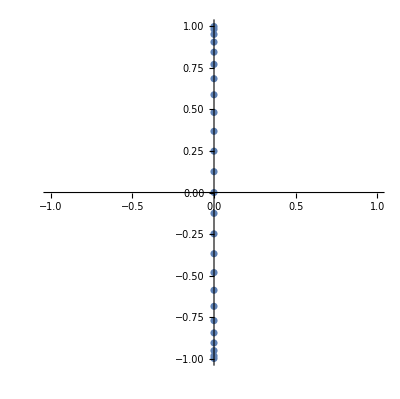

```mathematica
Dc= DiagonalMatrix[Table[1/(2 Δx),{i,1,n-1}],1] + DiagonalMatrix[Table[-1/(2 Δx),{i,1,n-1}],-1];
Dc[[1]
][[n]] = -1/(2 Δx);
Dc[[n]][[1]] = 1/(2 Δx);
Dc//MatrixForm;
Dcevals = Eigenvalues[Dc];
Dcz = Dcevals /. Δx -> 1;
csplot=ComplexListPlot[Dcz]
```

### Stability Overlap

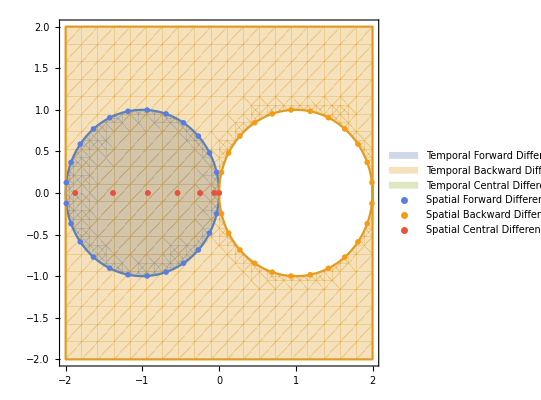

```mathematica
cfl = 1;
tforward = evalFE/.Δt-> cfl;
tbackward = evalBE/.Δt-> cfl;
tcentral = Re[γ Δt]/.Δt-> cfl;
ftplot= ComplexRegionPlot[Abs[tforward]≤ 1, {γ, -2-2 ⅈ, 2+2 ⅈ}];
btplot= ComplexRegionPlot[Abs[tbackward]≤ 1, {γ, -2-2 ⅈ, 2+2 ⅈ}];
ctplot= ComplexRegionPlot[Abs[tcentral]≤ 1, {γ, -2-2 ⅈ, 2+2 ⅈ}];
dotplot =ComplexListPlot[{Dpz,Dmz,Dcz},PlotTheme-> "Business",PlotLegends-> {"Spatial Forward Difference","Spatial Backward Difference","Spatial Central Difference"}];
combplot = ComplexRegionPlot[{Abs[tforward]≤ 1,Abs[tbackward]≤ 1,Re[γ]== 0.0}, {γ, -2-2 ⅈ, 2+2 ⅈ},PlotTheme-> "Automatic",PlotLegends-> {"Temporal Forward Difference","Temporal Backward Difference","Temporal Central Difference"}];

Show[{combplot,dotplot}]
```

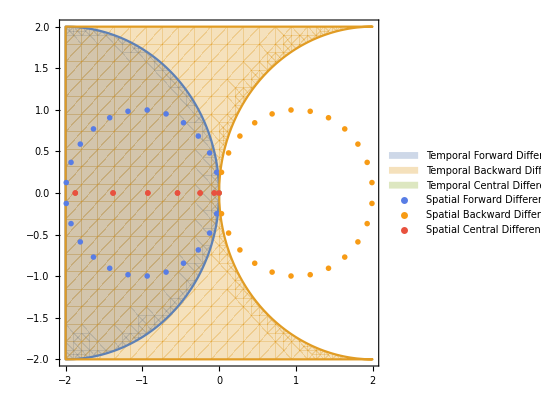

```mathematica
cfl = 0.5;
tforward = evalFE/.Δt-> cfl;
tbackward = evalBE/.Δt-> cfl;
tcentral = evals[[1]]/.Δt-> cfl;
ftplot= ComplexRegionPlot[Abs[tforward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
btplot= ComplexRegionPlot[Abs[tbackward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
ctplot= ComplexRegionPlot[Abs[tcentral]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
dotplot =ComplexListPlot[{Dpz,Dmz,Dcz},PlotTheme-> "Business",PlotLegends-> {"Spatial Forward Difference","Spatial Backward Difference","Spatial Central Difference"}];
combplot = ComplexRegionPlot[{Abs[tforward]≤ 1,Abs[tbackward]≤ 1,Re[γ]== 0.0}, {γ, -2-2 ⅈ, 2+2 ⅈ},PlotTheme-> "Automatic",PlotLegends-> {"Temporal Forward Difference","Temporal Backward Difference","Temporal Central Difference"}];

Show[{combplot,dotplot}]
```

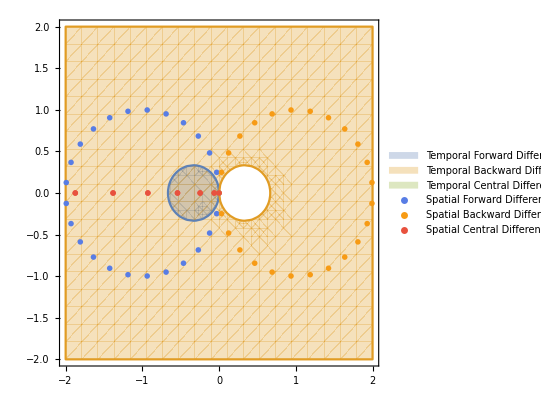

```mathematica
cfl = 3;
tforward = evalFE/.Δt-> cfl;
tbackward = evalBE/.Δt-> cfl;
tcentral = evals[[1]]/.Δt-> cfl;
ftplot= ComplexRegionPlot[Abs[tforward]≤ 1, {γ, -2-2 ⅈ, 2+2 ⅈ}];
btplot= ComplexRegionPlot[Abs[tbackward]≤ 1, {γ, -2-2 ⅈ, 2+2 ⅈ}];
ctplot= ComplexRegionPlot[Abs[tcentral]≤ 1, {γ, -2-2 ⅈ, 2+2 ⅈ}];
dotplot =ComplexListPlot[{Dpz,Dmz,Dcz},PlotTheme-> "Business",PlotLegends-> {"Spatial Forward Difference","Spatial Backward Difference","Spatial Central Difference"}];
combplot = ComplexRegionPlot[{Abs[tforward]≤ 1,Abs[tbackward]≤ 1,Re[γ]== 0.0}, {γ, -2-2 ⅈ, 2+2 ⅈ},PlotTheme-> "Automatic",PlotLegends-> {"Temporal Forward Difference","Temporal Backward Difference","Temporal Central Difference"}];

Show[{combplot,dotplot}]
```

### Part (iii)

The temporal stability regions will be identical to before, we just need to calculate the stability of the central difference second derivative in space.

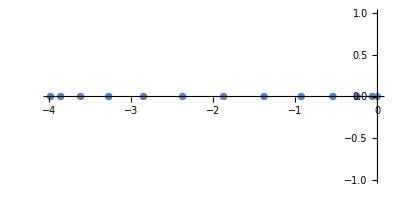

```mathematica
Dc= DiagonalMatrix[Table[-2/(Δx^2),{i,1,n}]]+DiagonalMatrix[Table[1/(Δx^2),{i,1,n-1}],1] + DiagonalMatrix[Table[1/(Δx^2),{i,1,n-1}],-1];
Dc[[1]
][[n]] = 1/(Δx^2);
Dc[[n]][[1]] = 1/(Δx^2);
Dc//MatrixForm;
Dcevals = Eigenvalues[Dc];
Dcz = Dcevals /. Δx -> 1;
csplot=ComplexListPlot[Dcz]
```

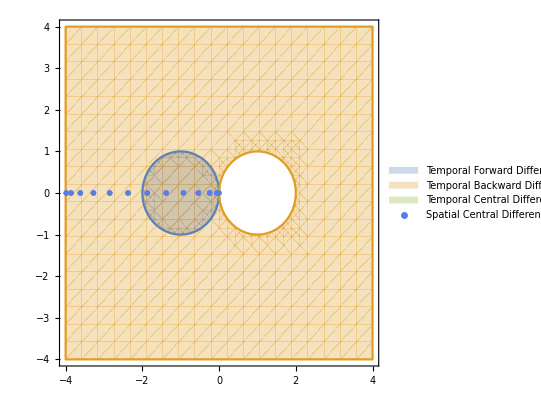

```mathematica
cfl = 1;
tforward = evalFE/.Δt-> cfl;
tbackward = evalBE/.Δt-> cfl;
tcentral = evals[[1]]/.Δt-> cfl;
ftplot= ComplexRegionPlot[Abs[tforward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
btplot= ComplexRegionPlot[Abs[tbackward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
ctplot= ComplexRegionPlot[Abs[tcentral]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
dotplot =ComplexListPlot[{Dcz},PlotTheme-> "Business",PlotLegends-> {"Spatial Central Difference"}];
combplot = ComplexRegionPlot[{Abs[tforward]≤ 1,Abs[tbackward]≤ 1,Re[γ]== 0.0}, {γ, -4-4 ⅈ, 4+4 ⅈ},PlotTheme-> "Automatic",PlotLegends-> {"Temporal Forward Difference","Temporal Backward Difference","Temporal Central Difference"}];

Show[{combplot,dotplot}]
```

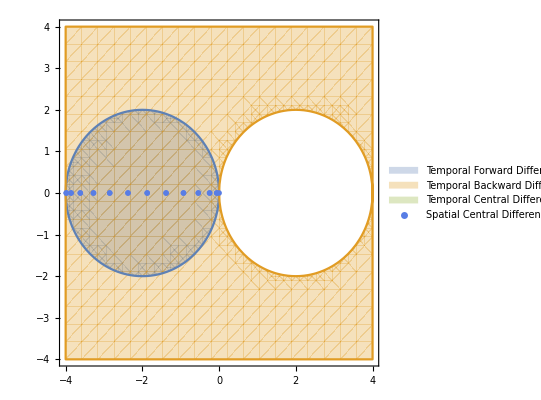

```mathematica
cfl = 0.5;
tforward = evalFE/.Δt-> cfl;
tbackward = evalBE/.Δt-> cfl;
tcentral = evals[[1]]/.Δt-> cfl;
ftplot= ComplexRegionPlot[Abs[tforward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
btplot= ComplexRegionPlot[Abs[tbackward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
ctplot= ComplexRegionPlot[Abs[tcentral]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
dotplot =ComplexListPlot[{Dcz},PlotTheme-> "Business",PlotLegends-> {"Spatial Central Difference"}];
combplot = ComplexRegionPlot[{Abs[tforward]≤ 1,Abs[tbackward]≤ 1,Re[γ]== 0.0}, {γ, -4-4 ⅈ, 4+4 ⅈ},PlotTheme-> "Automatic",PlotLegends-> {"Temporal Forward Difference","Temporal Backward Difference","Temporal Central Difference"}];

Show[{combplot,dotplot}]
```

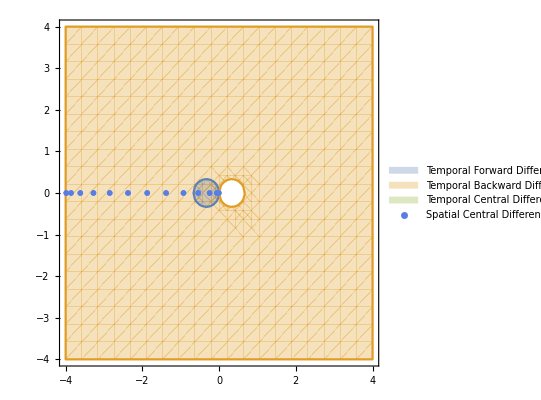

```mathematica
cfl = 3;
tforward = evalFE/.Δt-> cfl;
tbackward = evalBE/.Δt-> cfl;
tcentral = evals[[1]]/.Δt-> cfl;
ftplot= ComplexRegionPlot[Abs[tforward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
btplot= ComplexRegionPlot[Abs[tbackward]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
ctplot= ComplexRegionPlot[Abs[tcentral]≤ 1, {γ, -4-4 ⅈ, 4+4 ⅈ}];
dotplot =ComplexListPlot[{Dcz},PlotTheme-> "Business",PlotLegends-> {"Spatial Central Difference"}];
combplot = ComplexRegionPlot[{Abs[tforward]≤ 1,Abs[tbackward]≤ 1,Re[γ]== 0.0}, {γ, -4-4 ⅈ, 4+4 ⅈ},PlotTheme-> "Automatic",PlotLegends-> {"Temporal Forward Difference","Temporal Backward Difference","Temporal Central Difference"}];

Show[{combplot,dotplot}]
```